# Équation de Helmholtz II

(Les conditions frontières:X[0]=0 , ⅆ/ⅆx X[x]|)_(x=L)

## Équation d^2/dx^2 X(x)+k^2 X(x)=0

### La longueur

```mathematica
L:=2
```

### La phase initiale

```mathematica
α:=0
```

### Les valeurs propres

```mathematica
Subscript[k, n_]:=((n-1/2 )π)/L
```

```mathematica
Table[Subscript[k, n],{n,1,6}]
```

{π/4,(3 π)/4,(5 π)/4,(7 π)/4,(9 π)/4,(11 π)/4}

### Les fonctions propres

```mathematica
Subscript[X, n_][x_]=√(2/L)Sin[Subscript[k, n]  x+α]
```

Sin[1/2 (-1/2+n) π x]

```mathematica
Table[Subscript[X, n][x],{n,1,6}]
```

{Sin[(π x)/4],Sin[(3 π x)/4],Sin[(5 π x)/4],Sin[(7 π x)/4],Sin[(9 π x)/4],Sin[(11 π x)/4]}

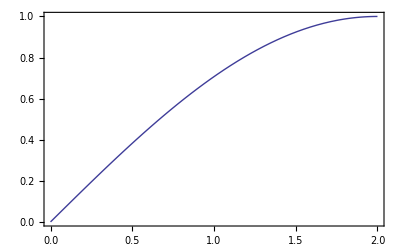
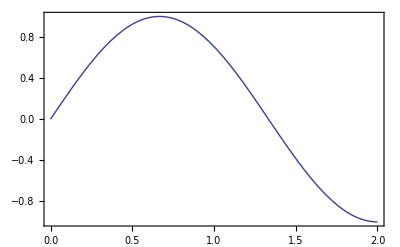
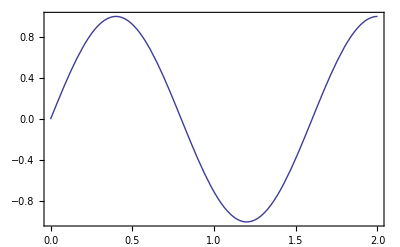
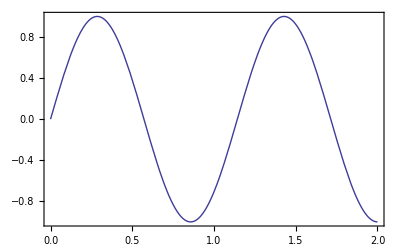
1 | π/4 | Sin[(π x)/4] | -Graphics-
2 | (3 π)/4 | Sin[(3 π x)/4] | -Graphics-
3 | (5 π)/4 | Sin[(5 π x)/4] | -Graphics-
4 | (7 π)/4 | Sin[(7 π x)/4] | -Graphics-

```mathematica
Table[{n,Subscript[k, n],Subscript[X, n][x],Plot[Subscript[X, n][x],{x,0,L},Frame->True]},{n,1,4}]//TableForm
```

### Solution Général

```mathematica
X[x_]=∑_(n=1)^6 Subscript[X, n][x]
```

Sin[(π x)/4]+Sin[(3 π x)/4]+Sin[(5 π x)/4]+Sin[(7 π x)/4]+Sin[(9 π x)/4]+Sin[(11 π x)/4]

```mathematica
Manipulate[∑_(n=1)^N Subscript[X, n][x],{N,1,20,1}]
```

```mathematica
Manipulate[Plot[∑_(n=1)^N Subscript[X, n][x],{x,0,L},AxesLabel->{"x","X(x)"},PlotLabel->Style[With[{N=N},HoldForm[X[x]=∑_(n=1)^N Subscript[X, n][x]]],12],PlotRange->{-2,15}],{N,1,20,1}]
```